```mathematica
ClearAll["Global`*"]

(*Gavish two-strain model*)(*Test cont with real bdAnalEx outputs*)(*Your setup*)RN={0->"S","S"+"I1"->2*"I1","S"+"Y1"->"Y1"+"I1","I1"->"R1","S"+"I2"->2*"I2","S"+"Y2"->"Y2"+"I2","I2"->"R2","R1"+"I2"->"I2"+"Y2","R1"+"Y2"->2*"Y2","Y2"->"R","R2"+"I1"->"I1"+"Y1","R2"+"Y1"->2*"Y1","Y1"->"R","R1"->"S","R2"->"S","R"->"S","S"->0,"I1"->0,"Y1"->0,"R1"->0,"I2"->0,"Y2"->0,"R2"->0,"R"->0};
rts={Λ,Subscript[β,1]*I1*S,Subscript[β,1]*Subscript[η,1]*Y1*S,Subscript[γ,1]*I1,Subscript[β,2]*I2*S,Subscript[β,2]*Subscript[η,2]*Y2*S,Subscript[γ,2]*I2,Subscript[β,2]*Subscript[σ,2]*I2*R1,Subscript[β,2]*Subscript[σ,2]*Subscript[η,2]*Y2*R1,Subscript[γ,2]*Y2,Subscript[β,1]*Subscript[σ,1]*I1*R2,Subscript[β,1]*Subscript[σ,1]*Subscript[η,1]*Y1*R2,Subscript[γ,1]*Y1,Subscript[θ,1]*R1,Subscript[θ,2]*R2,Subscript[θ,3]*R,μ*S,μ*I1,μ*Y1,μ*R1,μ*I2,μ*Y2,μ*R2,μ*R};
(*Get bdAnalEx outputs*)
bdAnal1[RN_, rts_, fval_,ins_: {}] := 
 Module[{spe, al, be, gam, Rv, RHS, def, var, cp, cv, ct, mS, mSi, inf, 
   mod, ng, K, eig, R0A, R0, cDFE, RDFE, eq0, var0, E0, cE0, EA, cEi, 
   RHSEi, eqEi, varEi, E1t, E2t, E1, E2, Jx, Jy, R12, R21, coP, par, 
   parSec, csi, eqI, findInstanceResult},
  
  {spe, al, be, gam, Rv, RHS, def} = extMat[RN];
  var = ToExpression[spe];
  RHS = gam . rts;
  par = Par[RHS, var];
  Print["RHS has var ", var, " par", par];
  cp = Thread[par > 0];
  cv = Thread[var >= 0];
  ct = Join[cp, cv];
  mS = minSiph[spe, asoRea[RN]];
  Print["minimal siphons ", mS, " Check siphon=", 
   isSiph[ToString /@ var, asoRea[RN], #] & /@ mS];
  
  (*Get infection species and NGM*)
  mSi = Map[Flatten[Position[spe, #] & /@ #] &, mS];
  inf = Union[Flatten[mSi]];
  Print["Infection species  at positions: ", inf];
  
  (*Compute DFE (E0)*)
  cDFE = Flatten[Thread[ToExpression[#] -> 0] & /@ mS];
  RDFE = RHS /. cDFE;
  eq0 = Thread[RDFE == 0];
  var0 = Complement[var, var[[inf]]];
  E0 = Join[Solve[eq0, var0] // Flatten, Thread[var[[inf]] -> 0]];
  cE0 = Select[Flatten[E0], (#[[2]] == 0) &];
  Print["DFE solution E0: ", E0];
  
  (*Compute reproduction numbers*)
  mod = {RHS, var, par};
  ng = NGM[mod, inf];
  Jx = ng[[1]] // FullSimplify /. Subscript[EpidCRN`Private`k, n_] :> Subscript[k, n];
  Jy = ng[[5]] // FullSimplify /. Subscript[EpidCRN`Private`k, n_] :> Subscript[k, n];
  K = ng[[4]] // FullSimplify /. Subscript[EpidCRN`Private`k, n_] :> Subscript[k, n];
  Print["NGM K= ", K // MatrixForm, " =", (K /. cDFE /. cE0) // MatrixForm];
  eig = K // Eigenvalues // Simplify;
  R0A = DeleteCases[eig, 0];(*Array of reproduction functions*)
  R0 = Max[R0A /. cDFE /. cE0] // FullSimplify;(*reproduction functions*)
  Print["Reproduction functions R0A: ", R0A];
  Print["R0 at DFE: ", R0];
  
  (*Compute boundary equilibria (EA)-equations and variables only*)
  EA = {};
  Do[(*For strain i boundary:set other strains to 0*)
   cEi = Thread[var[[Flatten[Delete[mSi, i]]]] -> 0];
   RHSEi = RHS /. cEi;
   eqEi = Thread[RHSEi == 0];
   varEi = var;(*All variables for this boundary system*)
   AppendTo[EA, {eqEi, varEi}], {i, mS // Length}];
  E1t = Solve[EA[[1]][[1]], EA[[1]][[2]]];
  E2t = Solve[EA[[2]][[1]], EA[[2]][[2]]];
  Print["Number of boundary systems= ", Length[EA], 
   " ;first sys has ", E1t // Length, " sols, E1 is ", 
   E1 = E1t[[2]] // Factor, " second sys has ", E2t // Length, 
   " sols, E2 is ", E2 = E2t[[2]] // Factor];
  R12 = R0A[[1]] /. E2 // Factor;
  R21 = R0A[[2]] /. E1 // Factor;
  
  (*Print["invasion curves intersect at ",eqI=Solve[R12== R21]];*)
  
  (* Handle parameter fixing based on ins *)
  If[ins === {} || Length[ins] == 0,
   (* Case: no parameters to fix *)
   coP = FindInstance[Join[cp, {(R12 ) > 1, (R21) > 1, 
   1<  (R0A[[1]] /. E0 ) ,1<  (R0A[[2]] /. E0 ),
   (R0A[[1]] /. E0 ) >  3(R0A[[2]] /. E0 )/2}], par] // Flatten,
   
   (* Case: some parameters to fix *)
   Print["Fixing parameters at positions: ", ins];
   csi = Thread[par[[ins]] -> fval];
   parSec = Delete[par, List /@ ins];
   
 (* Use FindInstance with constraints *)
   findInstanceResult = FindInstance[
     Join[Delete[cp, List /@ ins], {(R12 /. csi) > 1, (R21 /. csi) > 1, 
     1<  (R0A[[1]] /. E0/. csi ) ,1<  (R0A[[2]] /. E0 /. csi),
   (R0A[[1]] /. E0/. csi ) >  7(R0A[[2]] /. E0/. csi )/6,
   (R0A[[1]] /. E0 /. csi) >  3(R12/. csi )/2}], 
     parSec];
   
   (* Clean up context conflicts by replacing EpidCRN`Private symbols *)
   findInstanceResult = findInstanceResult /. 
     HoldPattern[Subscript[EpidCRN`Private`sym_, n_]] :> Subscript[sym, n];
   
   coP = Join[findInstanceResult // Flatten, csi];
   ];
  

  Print["under coP: ", coP," invasion nrs are", {R12, R21} /. coP//N,
  " repr nrs are",
  {(R0A[[1]] /. E0 ), (R0A[[2]] /. E0 )} /. coP//N ];
  
  {K, Jx, Jy, mSi, R0, R0A, E0, EA, E1, E2, RHS, var, cp, R12, R21, coP}
  ];

{ngm, Jx, Jy, mSi, R0, R0A, E0, EA, E1, E2, RHS, var, cp, R12, R21, coP(*,eqI*)} = bdAnal1[RN, rts,{1,1,10/4, 3},{7,8,12,13}];
```

bif param={β_1,β_2} coPsec = {Λ→2,μ→1/2,γ_1→1/16,γ_2→1,θ_1→1/2,θ_2→4,θ_3→1,η_1→1,η_2→1,σ_1→5/2,σ_2→3}p0={β_1→1/2,β_2→1}

R1s=R0A[[1]] /. E0  = (Λ β_1)/(μ (μ+γ_1))

R2s=R0A[[2]] /. E0  = (Λ β_2)/(μ (μ+γ_2))

R12s=R12 /. E2  = (β_1 (μ^3+2 μ^2 γ_2+μ γ_2^2+μ^2 θ_2+μ γ_2 θ_2-μ^2 γ_2 η_1 σ_1+Λ β_2 γ_2 η_1 σ_1-μ γ_2^2 η_1 σ_1))/(μ β_2 (μ+γ_1) (μ+γ_2+θ_2))

R21s=R21 /. E1   = (β_2 (μ^3+2 μ^2 γ_1+μ γ_1^2+μ^2 θ_1+μ γ_1 θ_1-μ^2 γ_1 η_2 σ_2+Λ β_1 γ_1 η_2 σ_2-μ γ_1^2 η_2 σ_2))/(μ β_1 (μ+γ_2) (μ+γ_1+θ_1))

p0 coordinates: {1/2,1} p1 coordinates: {1,1} p2 coordinates: {3/16,1}

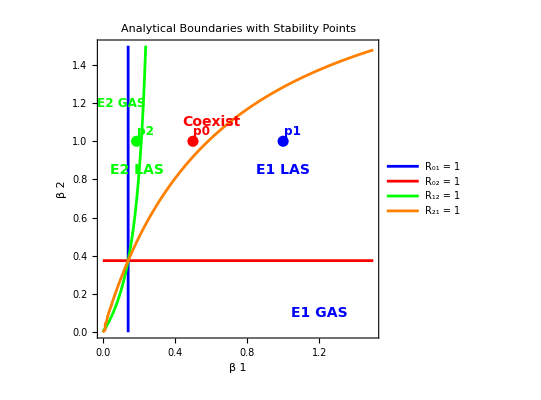

```mathematica
bifInd={3,4};
par=Par[RHS,var];
ploR[par_,coP_,R0A_,E0_,E1_,E2_,R12_,R21_,bifInd_:{1,2}]:=Module[{p0,coPsec,bifP,bifVars,eqs,eqL,p0Values,f1,f2,p1,p2,p1Values,p2Values},bifP=par[[bifInd]];
p0=coP[[bifInd]];
(*Remove β₁ and β₂ rules so ContourPlot can vary them*)coPsec=Delete[coP,List/@bifInd];
Print["bif param=",bifP," coPsec = ",coPsec,"p0=",p0];
Print["R1s=R0A[[1]] /. E0  = ",R1s=(R0A[[1]]/. E0)//Factor];
Print["R2s=R0A[[2]] /. E0  = ",R2s=(R0A[[2]]/. E0)//Factor];
Print["R12s=R12 /. E2  = ",R12s=(R12/. E2)//Factor];
Print["R21s=R21 /. E1   = ",R21s=(R21/. E1)//Factor];
eqL={R1s-1,R2s-1,R12s-1,R21s-1};
bifVars=Variables[eqL/. coPsec];
cp=Thread[bifVars>0];
eqs=Thread[(eqL/. coPsec)==0];
(*Use FindInstance for LAS E1 (strain 1 dominates)*)f1=FindInstance[Join[cp,{(R21/. E2/. coPsec)<1,1<(R0A[[1]]/. E0/. coPsec),1<(R0A[[2]]/. E0/. coPsec)}],bifVars];
p1=If[f1=!={},bifVars/. f1[[1]],{0.5,0.5}];
(*Use FindInstance for LAS E2 (strain 2 dominates)*)f2=FindInstance[Join[cp,{(R12/. E1/. coPsec)<1,1<(R0A[[1]]/. E0/. coPsec),1<(R0A[[2]]/. E0/. coPsec)}],bifVars];
p2=If[f2=!={},bifVars/. f2[[1]],{0.7,0.7}];
(*Extract numerical values*)p0Values=bifVars/. p0;
p1Values=p1;
p2Values=p2;
Print["p0 coordinates: ",p0Values," p1 coordinates: ",p1Values," p2 coordinates: ",p2Values];
ContourPlot[Evaluate[eqs],Evaluate@{bifVars[[1]],0,3/2},Evaluate@{bifVars[[2]],0,3/2},ContourStyle->{Blue,Red,Green,Orange},PlotLegends->{"R₀₁ = 1","R₀₂ = 1","R₁₂ = 1","R₂₁ = 1"},AxesLabel->{ToString[Subscript[β,1]],ToString[Subscript[β,2]]},PlotLabel->"Analytical Boundaries with Stability Points",Epilog->{PointSize[0.02],(*p0 point*)Red,Point[p0Values],Text[Style["p0",FontSize->12,FontWeight->Bold],p0Values+{0.05,0.05}],(*p1 point (strain 1 dominates)*)Blue,Point[p1Values],Text[Style["p1",FontSize->12,FontWeight->Bold],p1Values+{0.05,0.05}],(*p2 point (strain 2 dominates)*)Green,Point[p2Values],Text[Style["p2",FontSize->12,FontWeight->Bold],p2Values+{0.05,0.05}],(*Region labels*)(*E1 LAS region (near p1)*)Text[Style["E1 LAS",FontSize->14,FontWeight->Bold,FontColor->Blue],{p1Values[[1]],p1Values[[2]]-0.15}],(*E2 LAS region (near p2)*)Text[Style["E2 LAS",FontSize->14,FontWeight->Bold,FontColor->Green],{p2Values[[1]],p2Values[[2]]-0.15}],(*E1 GAS region (just above β₁ axis)*)Text[Style["E1 GAS",FontSize->14,FontWeight->Bold,FontColor->Blue],{1.2,0.1}],(*E2 GAS region (vertical downwards,near β₂ axis,smaller letters)*)Text[Style["E2 GAS",FontSize->12,FontWeight->Bold,FontColor->Green],{0.1,1.2},{0,-1}],(*Coexist region (around p0)*)Text[Style["Coexist",FontSize->14,FontWeight->Bold,FontColor->Red],{p0Values[[1]]+0.1,p0Values[[2]]+0.1}]}]]
ploR[par,coP, R0A, E0, E1, E2, R12, R21,bifInd]
```

```mathematica
ContourPlot[Evaluate[eqs],Sequence@@Thread[{bifP,{0,0},{2,2}}]//Evaluate,ContourStyle->{Blue,Red,Green,Orange},PlotLegends->{"R₀₁ = 1","R₀₂ = 1","R₁₂ = 1","R₂₁ = 1"},AxesLabel->{ToString[Subscript[β,1]],ToString[Subscript[β,2]]},PlotLabel->"Analytical Boundaries"]
```

ContourPlot::glims: Range specifications {vB,0,2} and {vB,0,2} contain the same iteration variable.

```mathematica
ContourPlot[eqs,{bifP,0,2},{bifP,0,2},ContourStyle->{Blue,Red,Green,Orange},PlotLegends->{"R₀₁ = 1","R₀₂ = 1","R₁₂ = 1","R₂₁ = 1"},AxesLabel->{ToString[Subscript[β, 1]],ToString[Subscript[β, 2]]},PlotLabel->"Analytical Boundaries"]
```

```mathematica
ploR[par_,coP_, R0A_, E0_, E1_, E2_, R12_, R21_,bifInd_:{1,2}] := 
  Block[{coPsec,bifP,eqs,eqL}, bifP=par[[bifInd]];
   (* Remove β₁ and β₂ rules so ContourPlot can vary them *)
   coPsec = Delete[coP, List/@bifInd];

      Print["bif param=",bifP," coPsec = ", coPsec];
Print["R1s=R0A[[1]] /. E0  = ", R1s=(R0A[[1]] /. E0) //Factor];
Print["R2s=R0A[[2]] /. E0  = ", R2s=(R0A[[2]] /. E0) //Factor];
Print["R12s=R12 /. E2  = ", R12s=(R12 /. E2) //Factor];
Print["R21s=R21 /. E1   = ", R21s=(R21 /. E1) //Factor];
eqL={R1s-1,R2s-1,R12s-1,R21s-1};bifP=Variables[eqL/. coPsec];
   eqs=Thread[(eqL/. coPsec)==0];
Print["eqs=",eqs,bifP,bifP==bifP];
  With[{β1=bifP[[1]],β2=bifP[[2]]},ContourPlot[eqs/. {Subscript[β,1]->β1,Subscript[β,2]->β2},{β1,0,2},{β2,0,2},ContourStyle->{Blue,Red,Green,Orange},PlotLegends->{"R₀₁ = 1","R₀₂ = 1","R₁₂ = 1","R₂₁ = 1"},AxesLabel->{"β₁","β₂"},PlotLabel->"Analytical Boundaries"]]
   ]
ploR[par,coP, R0A, E0, E1, E2, R12, R21,bifInd]
```

```mathematica
ploRI[par,coP_,R0A_,E0_,E1_,E2_,R12_,R21_,bifInd_]:=Module[{coP,plot,intersections,expr1,expr2,expr3,expr4,bifVar,int12,int13,int14,int23,int24,int34},
bifVar=par[[bifInd]];
(*The two bifurcation parameters*)Print["Bifurcation parameters: ",bifVar];
Print["Parameter set conditions: ",Short[coP,3]];
(*Define the four boundary expressions*)expr1=(R0A[[1]]/. E0/. coP)-1;(*R₀₁=1*)expr2=(R0A[[2]]/. E0/. coP)-1;(*R₀₂=1*)expr3=(R12/. E2/. coP)-1;(*R₁₂=1*)expr4=(R21/. E1/. coP)-1;(*R₂₁=1*)(*Find intersections of boundary curves*)int12=Quiet[Solve[{expr1==0,expr2==0},bifVar,Reals]];
int13=Quiet[Solve[{expr1==0,expr3==0},bifVar,Reals]];
int14=Quiet[Solve[{expr1==0,expr4==0},bifVar,Reals]];
int23=Quiet[Solve[{expr2==0,expr3==0},bifVar,Reals]];
int24=Quiet[Solve[{expr2==0,expr4==0},bifVar,Reals]];
int34=Quiet[Solve[{expr3==0,expr4==0},bifVar,Reals]];
intersections=Join[int12,int13,int14,int23,int24,int34];
intersections=DeleteCases[intersections,{}];
Print["Found ",Length[intersections]," boundary intersections"];
Do[Print["Intersection ",i,": ",intersections[[i]]],{i,1,Min[5,Length[intersections]]}];
(*Create contour plot*)plot=ContourPlot[{expr1==0,expr2==0,expr3==0,expr4==0},{bifVar[[1]],0,3},{bifVar[[2]],0,3},ContourStyle->{Blue,Red,Green,Orange},PlotLegends->{"R₀₁ = 1","R₀₂ = 1","R₁₂ = 1","R₂₁ = 1"},AxesLabel->{ToString[bifVar[[1]]],ToString[bifVar[[2]]]},PlotLabel->"Analytical Boundaries with Intersections"];
{plot,intersections}];

ploRI[par,coP,R0A,E0,E1,E2,R12,R21,bInd]
```

{Λ→3/2,μ→1,β_1→1,β_2→2,γ_1→1,γ_2→1,η_1→5,η_2→5/2,θ_1→1,θ_2→1/4,θ_3→1,σ_1→1,σ_2→1}

(β_1 (μ^3+2 μ^2 γ_2+μ γ_2^2+μ^2 θ_2+μ γ_2 θ_2-μ^2 γ_2 η_1 σ_1+Λ β_2 γ_2 η_1 σ_1-μ γ_2^2 η_1 σ_1))/(μ β_2 (μ+γ_1) (μ+γ_2+θ_2))

Module::lvsym: Local variable specification {{Λ→3/2,μ→1,β_1→1,β_2→2,γ_1→1,γ_2→1,η_1→5,η_2→5/2,θ_1→1,θ_2→1/4,«3»},plot$,intersections$,expr1$,expr2$,expr3$,expr4$,bifVar$,int12$,int13$,«4»} contains {Λ→3/2,μ→1,β_1→1,β_2→2,γ_1→1,γ_2→1,η_1→5,η_2→5/2,θ_1→1,θ_2→1/4,«3»}, which is not a symbol or an assignment to a symbol.

Module[{{Λ→3/2,μ→1,β_1→1,β_2→2,γ_1→1,γ_2→1,η_1→5,η_2→5/2,θ_1→1,θ_2→1/4,θ_3→1,σ_1→1,σ_2→1},plot$,intersections$,expr1$,expr2$,expr3$,expr4$,bifVar$,int12$,int13$,int14$,int23$,int24$,int34$},bifVar$=par⟦{3,4}⟧;Print[Bifurcation parameters: ,bifVar$];Print[Parameter set conditions: ,{Λ→3/2,μ→1,β_1→1,β_2→2,γ_1→1,γ_2→1,η_1→5,η_2→5/2,θ_1→1,θ_2→1/4,θ_3→1,σ_1→1,σ_2→1}];expr1$=({(β_1 (S+R2 η_1 σ_1))/(μ+γ_1),(β_2 (S+R1 η_2 σ_2))/(μ+γ_2)}⟦1⟧/.{R→0,R1→0,R2→0,S→Λ/μ,I1→0,Y1→0,I2→0,Y2→0}/.{Λ→3/2,μ→1,β_1→1,β_2→2,γ_1→1,γ_2→1,η_1→5,η_2→5/2,θ_1→1,θ_2→1/4,θ_3→1,σ_1→1,σ_2→1})-1;expr2$=({(β_1 (S+R2 η_1 σ_1))/(μ+γ_1),(β_2 (S+R1 η_2 σ_2))/(μ+γ_2)}⟦2⟧/.{R→0,R1→0,R2→0,S→Λ/μ,I1→0,Y1→0,I2→0,Y2→0}/.{Λ→3/2,μ→1,β_1→1,β_2→2,γ_1→1,γ_2→1,η_1→5,η_2→5/2,θ_1→1,θ_2→1/4,θ_3→1,σ_1→1,σ_2→1})-1;expr3$=((β_1 (μ^3+2 μ^2 γ_2+μ γ_2^2+μ^2 θ_2+μ γ_2 θ_2-μ^2 γ_2 η_1 σ_1+Λ β_2 γ_2 η_1 σ_1-μ γ_2^2 η_1 σ_1))/(μ β_2 (μ+γ_1) (μ+γ_2+θ_2))/.{S→(μ+γ_2)/β_2,R1→0,I2→-((μ^2-Λ β_2+μ γ_2) (μ+θ_2))/(μ β_2 (μ+γ_2+θ_2)),Y2→0,R2→-(γ_2 (μ^2-Λ β_2+μ γ_2))/(μ β_2 (μ+γ_2+θ_2)),R→0}/.{Λ→3/2,μ→1,β_1→1,β_2→2,γ_1→1,γ_2→1,η_1→5,η_2→5/2,θ_1→1,θ_2→1/4,θ_3→1,σ_1→1,σ_2→1})-1;expr4$=((β_2 (μ^3+2 μ^2 γ_1+μ γ_1^2+μ^2 θ_1+μ γ_1 θ_1-μ^2 γ_1 η_2 σ_2+Λ β_1 γ_1 η_2 σ_2-μ γ_1^2 η_2 σ_2))/(μ β_1 (μ+γ_2) (μ+γ_1+θ_1))/.{S→(μ+γ_1)/β_1,I1→-((μ^2-Λ β_1+μ γ_1) (μ+θ_1))/(μ β_1 (μ+γ_1+θ_1)),Y1→0,R1→-(γ_1 (μ^2-Λ β_1+μ γ_1))/(μ β_1 (μ+γ_1+θ_1)),R2→0,R→0}/.{Λ→3/2,μ→1,β_1→1,β_2→2,γ_1→1,γ_2→1,η_1→5,η_2→5/2,θ_1→1,θ_2→1/4,θ_3→1,σ_1→1,σ_2→1})-1;int12$=Quiet[Solve[{expr1$==0,expr2$==0},bifVar$,ℝ]];int13$=Quiet[Solve[{expr1$==0,expr3$==0},bifVar$,ℝ]];int14$=Quiet[Solve[{expr1$==0,expr4$==0},bifVar$,ℝ]];int23$=Quiet[Solve[{expr2$==0,expr3$==0},bifVar$,ℝ]];int24$=Quiet[Solve[{expr2$==0,expr4$==0},bifVar$,ℝ]];int34$=Quiet[Solve[{expr3$==0,expr4$==0},bifVar$,ℝ]];intersections$=Join[int12$,int13$,int14$,int23$,int24$,int34$];intersections$=DeleteCases[intersections$,{}];Print[Found ,Length[intersections$], boundary intersections];Do[Print[Intersection ,i,: ,intersections$⟦i⟧],{i,1,Min[5,Length[intersections$]]}];plot$=ContourPlot[{expr1$==0,expr2$==0,expr3$==0,expr4$==0},{bifVar$⟦1⟧,0,3},{bifVar$⟦2⟧,0,3},ContourStyle→{Blue,Red,Green,Orange},PlotLegends→{R₀₁ = 1,R₀₂ = 1,R₁₂ = 1,R₂₁ = 1},AxesLabel→{ToString[bifVar$⟦1⟧],ToString[bifVar$⟦2⟧]},PlotLabel→Analytical Boundaries with Intersections];{plot$,intersections$}]

```mathematica
bifPl[RHS_,var_,coP_,par_,bifInd_,startPoint_,ranges_,gridSize_:20]:=Module[{scanResults,hopfBoundary,hopfPlot,stableCount,unstableCount},Print["Starting bifurcation analysis from point: ",startPoint];
Print["Parameter ranges: ",ranges];
Print["Scanning (",gridSize,"×",gridSize," grid)..."];
(*Use the existing scanPar with proper parameter handling*)scanResults=scanPar[RHS,var,coP,par,bifInd,ranges,gridSize];
(*Count results*)stableCount=Length[Select[scanResults,#["Region"]==="Stable"&]];
unstableCount=Length[Select[scanResults,#["Region"]==="Unstable"&]];
Print["Stability summary around intersection:"];
Print["Stable: ",stableCount,", Unstable: ",unstableCount];
Print["No equilibrium: ",Length[Select[scanResults,#["Region"]==="NoEq"&]]];
(*Extract Hopf boundary*)hopfBoundary=extractHopfBoundary[scanResults];
Print["Found ",Length[hopfBoundary]," Hopf boundary points"];
(*Create plots*)If[Length[hopfBoundary]>0,hopfPlot=ListPlot[hopfBoundary,PlotStyle->{Black,PointSize[0.02]},PlotLegends->{"Hopf bifurcation"},AxesLabel->{ToString[par[[bifInd[[1]]]]],ToString[par[[bifInd[[2]]]]]},PlotLabel->"Hopf Boundary near Intersection"];
{scanResults,hopfPlot},Print["No Hopf boundary detected - try expanding ranges"];
{scanResults,{}}]];

(*Function to generate ranges around intersection point*)
generateRangesAroundPoint[point_,radius_:0.2]:=Module[{center1,center2},center1=point[[1]][[2]];(*First parameter value*)center2=point[[2]][[2]];(*Second parameter value*){{center1-radius,center1+radius},{center2-radius,center2+radius}}];


(*
===USAGE EXAMPLE===(*1. Set up parameters as suggested*)ins={12,13};
csi=Thread[par[[ins]]->{10/4,3}];
(*2. Create new parameter set*)coPNew=Join[Delete[coP,ins],csi];
(*3. Find analytical boundaries and intersections*){analyticalPlot,intersections}=ploRI[coPNew,R0A,E0,E1,E2,R12,R21,ins];
(*4. Choose an intersection point and generate ranges*)If[Length[intersections]>0,startPoint=intersections[[1]];(*Pick first intersection*)ranges=generateRangesAroundPoint[startPoint,0.15];(*Small radius around intersection*)Print["Using intersection: ",startPoint];
Print["Generated ranges: ",ranges];
(*5. Run bifurcation analysis*)bifInd=ins;(*Bifurcation parameter indices*){scanResults,hopfPlot}=bifPl[RHS,var,coPNew,par,bifInd,startPoint,ranges,15];
(*6. Combine analytical and numerical results*)Show[analyticalPlot,hopfPlot],Print["No intersections found - check parameter ranges"];];*)

(*Alternative:Manual starting point*)
(*startPoint={{par[[ins[[1]]]],2.0},{par[[ins[[2]]]],2.5}};*)
(*ranges=generateRangesAroundPoint[startPoint,0.2];*)
```

```mathematica
"ploRI[coP, R0A, E0, E1, E2, R12, R21, ins] plots analytical boundaries and finds intersections"
```

bifPl[RHS, var, coP, par, bifInd, startPoint, ranges, gridSize] performs bifurcation analysis starting from intersection point

{Λ→3/2,μ→1,β_1→1,β_2→2,γ_1→1,γ_2→1,η_1→3,η_2→3/2,θ_1→1,θ_2→1,θ_3→1,σ_1→5/2,σ_2→3}

Bifurcation parameters: {σ_1,σ_2}

Parameter set (excluding bifurcation params): {Λ→3/2,μ→1,β_1→1,β_2→2,γ_1→1,γ_2→1,η_1→3,η_2→3/2,θ_1→1,θ_2→1,θ_3→1}

Found 1 boundary intersections

Intersection 1: {σ_1→2,σ_2→4}

StringForm::sfr: Item 2 requested in "`1` cannot be interpreted. The operator `2` requires a subscript with a variable specification." out of range; 1 items available.

Internal`LocalizedBlock::novar: bifVars$58748⟦1⟧ cannot be interpreted. The operator `2` requires a subscript with a variable specification.

```mathematica
ploR::usage = "ploR[coP, R0A, E0, E1, E2, R12, R21] plots analytical boundaries from reproduction numbers";
bifPl::usage="bifPl[RHS, var, coP, par, bifInd, startPoint, ranges, gridSize] performs bifurcation analysis starting from intersection point"
```